```mathematica
(********* Ex. 1   y'= Exp[-x]-2y   **********)
```

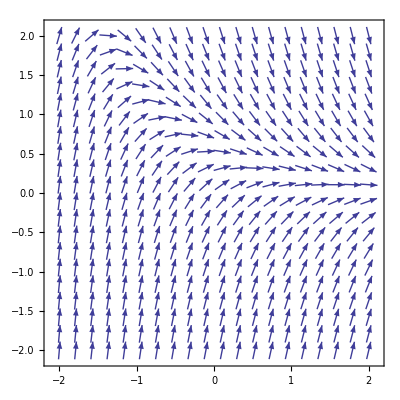

```mathematica
vp1=VectorPlot[{1,Exp[-x]-2 y},{x,-2,2},{y,-2,2},VectorStyle->Arrowheads[0.01],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20]
```

```mathematica
sol1=DSolve[y'[x]==Exp[-x] -2 y[x],y[x],x]
```

{{y[x]→ⅇ^-x+ⅇ^(-2 x) C[1]}}

```mathematica
sol1[[1,1,2]]
```

ⅇ^-x+ⅇ^(-2 x) C[1]

```mathematica
table1=Table[sol1[[1,1,2]]/.C[1]->a,{a,-2,2,.5}]
```

{-2. ⅇ^(-2 x)+ⅇ^-x,-1.5 ⅇ^(-2 x)+ⅇ^-x,-1. ⅇ^(-2 x)+ⅇ^-x,-0.5 ⅇ^(-2 x)+ⅇ^-x,0. ⅇ^(-2 x)+ⅇ^-x,0.5 ⅇ^(-2 x)+ⅇ^-x,1. ⅇ^(-2 x)+ⅇ^-x,1.5 ⅇ^(-2 x)+ⅇ^-x,2. ⅇ^(-2 x)+ⅇ^-x}

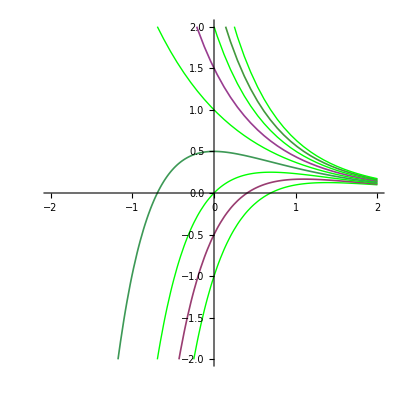

```mathematica
p1=Plot[Evaluate[table1],{x,-2,2},PlotRange->{-2,2},AspectRatio->Automatic,PlotStyle->{Green,Thickness[.003]}]
```

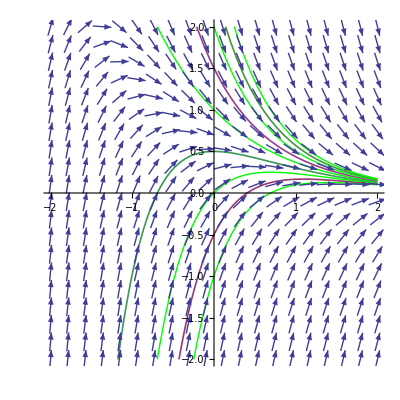

```mathematica
Show[p1,vp1]
```

```mathematica
(********* Ex. 2   y'= -y/x   **********)
```

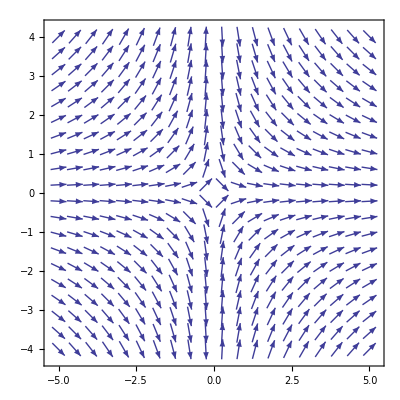

```mathematica
vp2=VectorPlot[{1,-y/x},{x,-5,5},{y,-4,4},VectorStyle->Arrowheads[.01],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20]
```

```mathematica
sol2=DSolve[y'[x]==-y[x]/x,y[x],x]
```

{{y[x]→C[1]/x}}

```mathematica
sol2[[1,1,2]]
```

C[1]/x

```mathematica
table2=Table[sol2[[1,1,2]]/.C[1]->a,{a,-3,3,.5}]
```

{-3./x,-2.5/x,-2./x,-1.5/x,-1./x,-0.5/x,0./x,0.5/x,1./x,1.5/x,2./x,2.5/x,3./x}

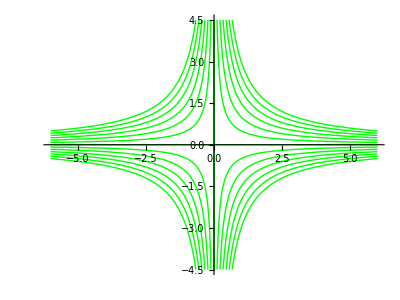

```mathematica
p2=Plot[Evaluate[table2],{x,-6,6},PlotRange->{-4.5,4.5},AspectRatio->Automatic,PlotStyle->Directive[Green,Thickness[.0025]]]
```

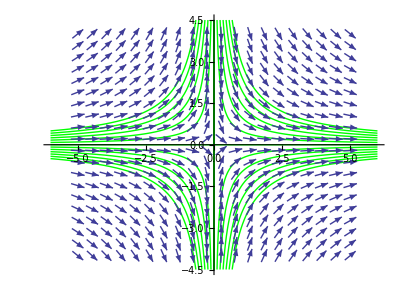

```mathematica
Show[p2,vp2]
```

```mathematica
(********* Ex. 3   y'= -x/y   **********)
```

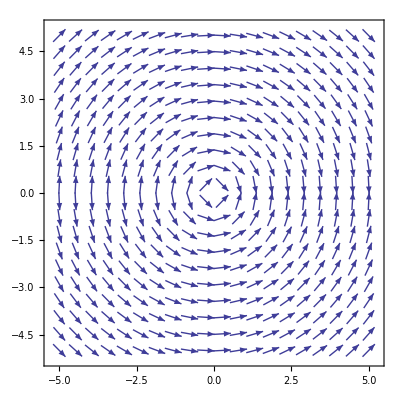

```mathematica
vp3=VectorPlot[{1,-x/y},{x,-5,5},{y,-5,5},VectorStyle->Arrowheads[.01],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20]
```

```mathematica
sol3=DSolve[y'[x]==-x/y[x],y[x],x]
```

{{y[x]→-√(-x^2+2 C[1])},{y[x]→√(-x^2+2 C[1])}}

```mathematica
sol3[[2,1,2]]
```

√(-x^2+2 C[1])

```mathematica
table3=Table[sol3[[2,1,2]]/.C[1]->a,{a,0,5,.5}]
```

{√(0.-x^2),√(1.-x^2),√(2.-x^2),√(3.-x^2),√(4.-x^2),√(5.-x^2),√(6.-x^2),√(7.-x^2),√(8.-x^2),√(9.-x^2),√(10.-x^2)}

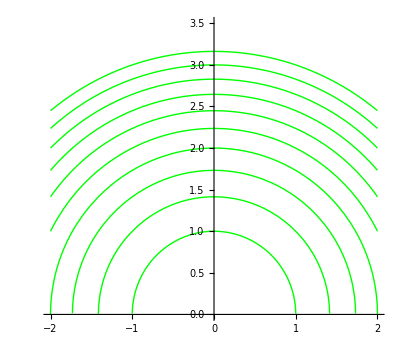

```mathematica
p3=Plot[Evaluate[table3],{x,-2,2},PlotRange->{0,3.5},AspectRatio->Automatic,PlotStyle->{Green}]
```

```mathematica
expression=x^2+y^2==C
```

x^2+y^2==C

```mathematica
table31=Table[expression/.C->a,{a,1,25,2}]
```

{x^2+y^2==1,x^2+y^2==3,x^2+y^2==5,x^2+y^2==7,x^2+y^2==9,x^2+y^2==11,x^2+y^2==13,x^2+y^2==15,x^2+y^2==17,x^2+y^2==19,x^2+y^2==21,x^2+y^2==23,x^2+y^2==25}

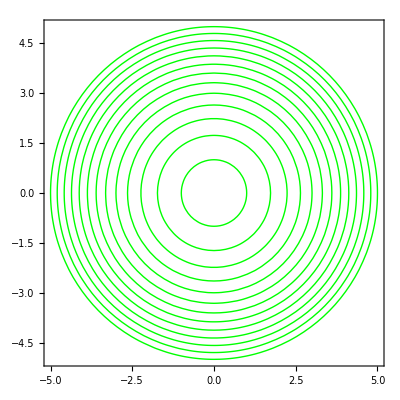

```mathematica
p31=ContourPlot[Evaluate[table31],{x,-5,5},{y,-5,5},ContourStyle->Directive[Green,Thickness[.0025]]]
```

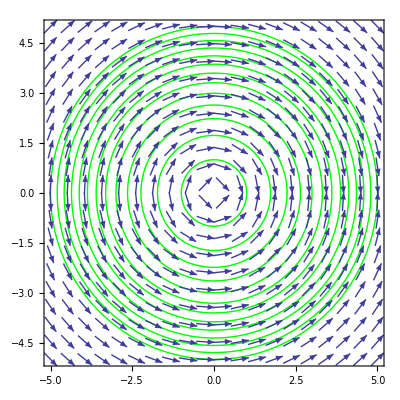

```mathematica
Show[p31,vp3]
```

```mathematica
(********* Ex. 4   y'= Sqrt[y]  **********)
```

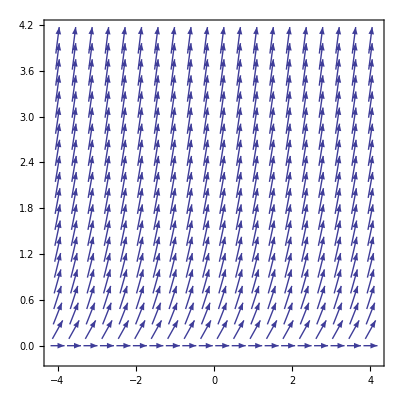

```mathematica
vp4=VectorPlot[{1,2 Sqrt[y]},{x,-4,4},{y,0,4},VectorStyle->Arrowheads[0.01],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20]
```

```mathematica
sol4=DSolve[y'[x]==2 Sqrt[y[x]],y[x],x]
```

{{y[x]→1/4 (4 x^2+4 x C[1]+C[1]^2)}}

```mathematica
sol4[[1,1,2]]
```

1/4 (4 x^2+4 x C[1]+C[1]^2)

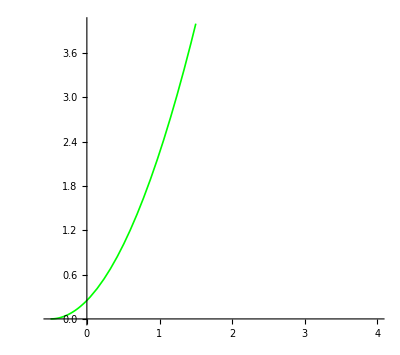

```mathematica
p41=Plot[sol4[[1,1,2]]/.C[1]->1,{x,-.5,4},AspectRatio->Automatic,PlotStyle->{Green,Thickness[.003]},PlotRange->{0,4}]
```

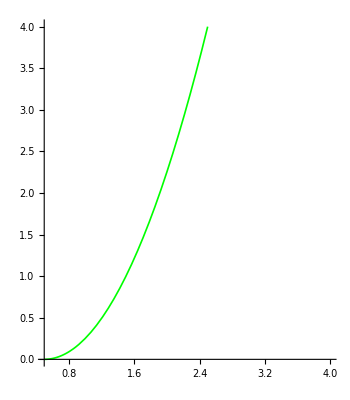

```mathematica
p42=Plot[sol4[[1,1,2]]/.C[1]->-1,{x,0.5,4},AspectRatio->Automatic,PlotStyle->{Green,Thickness[.003]},PlotRange->{0,4}]
```

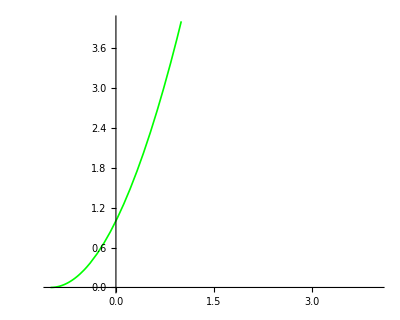

```mathematica
p43=Plot[sol4[[1,1,2]]/.C[1]->2,{x,-1,4},AspectRatio->Automatic,PlotStyle->{Green,Thickness[.003]},PlotRange->{0,4}]
```

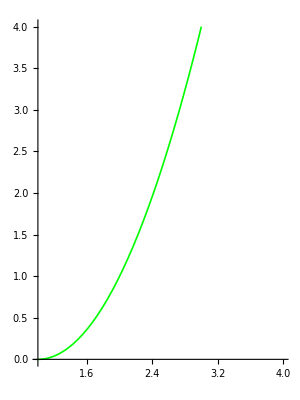

```mathematica
p44=Plot[sol4[[1,1,2]]/.C[1]->-2,{x,1,4},AspectRatio->Automatic,PlotStyle->{Green,Thickness[.003]},PlotRange->{0,4}]
```

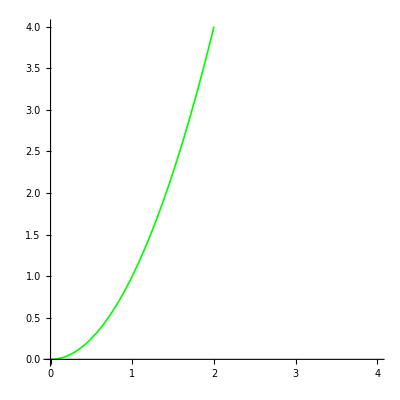

```mathematica
p45=Plot[sol4[[1,1,2]]/.C[1]->0,{x,0,4},AspectRatio->Automatic,PlotStyle->{Green,Thickness[.003]},PlotRange->{0,4}]
```

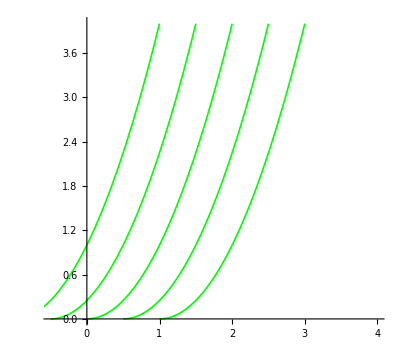

```mathematica
Show[p41,p42,p43,p44,p45]
```

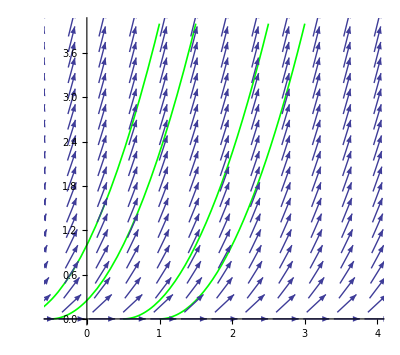

```mathematica
Show[p41,p42,p43,p44,vp4]
```

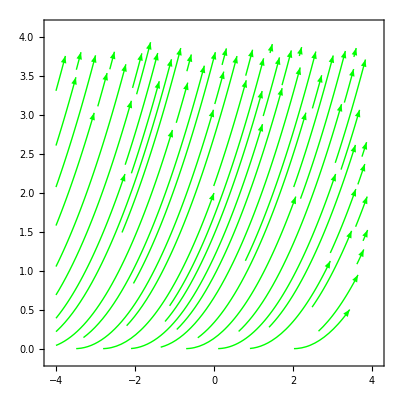

```mathematica
StreamPlot[{1,Sqrt[y]},{x,-4,4},{y,0,4},StreamScale->{Fine},StreamStyle->{Green,Arrowheads[.02]},StreamPoints->60]
```